```mathematica
f=Import["C:\\Users\\kahrendsen2\\Box Sync\\Research\\DataRuns\\othePeopleData\\willDichrosim\\HP Light AOI 10.csv"];
```

```mathematica
SetDirectory["C:\\Users\\kahrendsen2\\Box Sync\\Research\\DataRuns\\othePeopleData\\willDichrosim\\"]
```

C:\Users\kahrendsen2\Box Sync\Research\DataRuns\othePeopleData\willDichrosim

```mathematica
value=Take[f,{2,-1}];
t=Transpose[value];
steps=t[[1]];
angles=t[[2]];
voltage=t[[3]];
rotateValue=Ceiling[Length[steps]/4];
rotated=RotateLeft[voltage,rotateValue];
dichroism=(voltage-rotated)/(voltage+rotated)
newData=Transpose[{Prepend[steps,"steps"],Prepend[angles,"angles"],Prepend[voltage,"voltage"],Prepend[dichroism,"dichroism"]}]
Export["HP Light AOI 10_RotationalDichroism.csv",newData]
```

{-0.0107527,-0.0162162,-0.0108696,-0.0107527,-0.0054054,-0.0107527,-0.0107527,-0.0054054,-0.0054054,-0.0162162,-0.0108696,-0.0054054,-0.0107527,-0.0054054,-0.0054054,-0.0107527,-0.0054054,-0.0107527,-0.0054054,-0.0054054,0.,-0.00546448,0.,-0.00546448,0.,0.,0.,0.,0.00546448,0.00546448,0.,0.00546448,0.00546448,0.0108696,0.0108696,0.0108696,0.0054054,0.0108696,0.0054054,0.0108696,0.0054054,0.0054054,0.0054054,0.0108696,0.0162162,0.0162162,0.0108696,0.0054054,0.0162162,0.0108696,0.0108696,0.0108696,0.0054054,0.0108696,0.0162162,0.0054054,0.0054054,0.0108696,0.0054054,0.0108696,0.0108696,0.0107527,0.0107527,0.0107527,0.0107527,0.0107527,0.00534759,0.,0.,0.0054054,0.,0.00534759,0.0054054,0.,0.00534759,0.,0.,0.,0.,0.00534759,0.,0.,0.00534759,-0.00534759,0.00534759,0.,0.00534759,0.00534759,0.,0.00534759,0.,0.00534759,0.,0.00534759,0.00534759,0.,0.,0.00534759,0.,0.,0.00534759,0.,0.,0.0107527,0.0054054,0.0107527,0.0054054,0.0054054,0.,-0.0054054,0.,0.00546448,0.,0.,-0.00546448,-0.00546448,-0.00546448,-0.00546448,0.,-0.00546448,-0.00546448,-0.0108696,-0.0108696,-0.0108696,-0.0054054,-0.0108696,-0.0054054,-0.0108696,-0.0054054,0.,-0.0054054,-0.0108696,-0.00546448,-0.00546448,-0.0108696,0.,-0.00546448,-0.0108696,-0.0108696,-0.00546448,-0.0054054,-0.00546448,-0.00546448,-0.0054054,0.,-0.00546448,-0.0054054,-0.00546448,-0.0108696,0.,-0.0054054,-0.0054054,-0.0054054,-0.0054054,0.,0.,0.,-0.0054054,0.,0.,-0.0054054,0.,0.,0.,0.,-0.00534759,-0.00534759,0.,-0.00534759,-0.00534759,0.,0.00534759,0.,0.,-0.00534759,-0.00534759,0.,-0.00534759,-0.00534759,-0.00534759,-0.00534759,-0.00534759,-0.00534759,-0.00534759,-0.00534759,0.,-0.00534759,-0.00534759,-0.00534759,-0.00534759,-0.00534759,-0.0107527,-0.0107527,-0.0107527,-0.0107527,-0.0054054,-0.0107527,-0.00534759,-0.0107527,-0.0162162,-0.0107527,-0.0162162,-0.0054054,-0.0054054,-0.0054054,0.,-0.0054054,-0.0054054,-0.0054054,0.,0.,0.,0.0054054,0.0054054,0.,0.,0.0054054,0.,0.0054054,0.0054054,0.,0.,0.0054054,0.,0.,0.0054054,0.,-0.0054054,0.0054054,-0.0054054,0.,0.0054054,0.,0.,0.0054054,-0.0054054,0.,0.,0.0054054,0.,0.0054054,0.0054054,0.,0.0054054,0.0054054,0.0054054,0.0054054,0.0054054,0.0054054,0.0054054,0.0054054,0.0108696,0.0054054,0.0107527,0.0107527,0.0054054,0.0162162,0.0107527,0.0054054,0.0108696,0.0054054,0.0054054,0.0107527,0.0162162,0.0162162,0.0107527,0.0107527,0.0107527,0.0107527,0.0107527,0.0107527,0.0162162,0.0162162,0.0054054,0.0107527,0.0107527,0.0107527,0.0107527,0.0107527,0.0107527,0.0107527,0.0107527,0.0107527,0.0108696,0.0107527,0.0162162,0.0107527,0.0162162,0.0162162,0.0162162,0.0054054,0.0054054,0.0054054,0.,0.0054054,0.,0.,0.,0.,0.,-0.0054054,-0.0054054,0.,0.,-0.0054054,-0.0054054,-0.0107527,-0.0107527,-0.0054054,-0.0054054,-0.0107527,-0.0054054,-0.0054054,-0.0054054,0.,0.,-0.0107527,0.,-0.0054054,-0.0054054,-0.0054054,-0.0054054,-0.0054054,-0.00534759,-0.00534759,-0.0107527,-0.0107527,-0.00534759,-0.0107527,-0.0054054,0.,-0.0054054,-0.0054054,-0.0107527,-0.0054054,-0.0054054,-0.0107527,-0.0054054,-0.0054054,-0.0108696,-0.0054054,-0.0107527,-0.0054054,-0.0054054,-0.0162162,-0.0054054,-0.0107527,-0.0108696,-0.0107527,-0.0107527}

{{steps,angles,voltage,dichroism},{0.,0.,0.224609,-0.0107527},{1.,1.02857,0.222168,-0.0162162},{2.,2.05714,0.222168,-0.0108696},{3.,3.08571,0.224609,-0.0107527},{4.,4.11429,0.224609,-0.0054054},{5.,5.14286,0.224609,-0.0107527},{6.,6.17143,0.224609,-0.0107527},{7.,7.2,0.224609,-0.0054054},{8.,8.22857,0.224609,-0.0054054},{9.,9.25714,0.222168,-0.0162162},{10.,10.2857,0.222168,-0.0108696},{11.,11.3143,0.224609,-0.0054054},{12.,12.3429,0.224609,-0.0107527},{13.,13.3714,0.224609,-0.0054054},{14.,14.4,0.224609,-0.0054054},{15.,15.4286,0.224609,-0.0107527},{16.,16.4571,0.224609,-0.0054054},{17.,17.4857,0.224609,-0.0107527},{18.,18.5143,0.224609,-0.0054054},{19.,19.5429,0.224609,-0.0054054},{20.,20.5714,0.224609,0.},{21.,21.6,0.222168,-0.00546448},{22.,22.6286,0.224609,0.},{23.,23.6571,0.222168,-0.00546448},{24.,24.6857,0.224609,0.},{25.,25.7143,0.222168,0.},{26.,26.7429,0.222168,0.},{27.,27.7714,0.222168,0.},{28.,28.8,0.224609,0.00546448},{29.,29.8286,0.224609,0.00546448},{30.,30.8571,0.224609,0.},{31.,31.8857,0.224609,0.00546448},{32.,32.9143,0.224609,0.00546448},{33.,33.9429,0.227051,0.0108696},{34.,34.9714,0.227051,0.0108696},{35.,36.,0.227051,0.0108696},{36.,37.0286,0.227051,0.0054054},{37.,38.0571,0.227051,0.0108696},{38.,39.0857,0.227051,0.0054054},{39.,40.1143,0.227051,0.0108696},{40.,41.1429,0.227051,0.0054054},{41.,42.1714,0.227051,0.0054054},{42.,43.2,0.227051,0.0054054},{43.,44.2286,0.227051,0.0108696},{44.,45.2571,0.229492,0.0162162},{45.,46.2857,0.229492,0.0162162},{46.,47.3143,0.227051,0.0108696},{47.,48.3429,0.227051,0.0054054},{48.,49.3714,0.229492,0.0162162},{49.,50.4,0.227051,0.0108696},{50.,51.4286,0.227051,0.0108696},{51.,52.4571,0.227051,0.0108696},{52.,53.4857,0.227051,0.0054054},{53.,54.5143,0.227051,0.0108696},{54.,55.5429,0.229492,0.0162162},{55.,56.5714,0.227051,0.0054054},{56.,57.6,0.227051,0.0054054},{57.,58.6286,0.227051,0.0108696},{58.,59.6571,0.227051,0.0054054},{59.,60.6857,0.227051,0.0108696},{60.,61.7143,0.227051,0.0108696},{61.,62.7429,0.229492,0.0107527},{62.,63.7714,0.229492,0.0107527},{63.,64.8,0.229492,0.0107527},{64.,65.8286,0.229492,0.0107527},{65.,66.8571,0.229492,0.0107527},{66.,67.8857,0.229492,0.00534759},{67.,68.9143,0.227051,0.},{68.,69.9429,0.227051,0.},{69.,70.9714,0.227051,0.0054054},{70.,72.,0.227051,0.},{71.,73.0286,0.229492,0.00534759},{72.,74.0571,0.227051,0.0054054},{73.,75.0857,0.227051,0.},{74.,76.1143,0.229492,0.00534759},{75.,77.1429,0.227051,0.},{76.,78.1714,0.227051,0.},{77.,79.2,0.227051,0.},{78.,80.2286,0.227051,0.},{79.,81.2571,0.229492,0.00534759},{80.,82.2857,0.227051,0.},{81.,83.3143,0.227051,0.},{82.,84.3429,0.229492,0.00534759},{83.,85.3714,0.227051,-0.00534759},{84.,86.4,0.229492,0.00534759},{85.,87.4286,0.227051,0.},{86.,88.4571,0.229492,0.00534759},{87.,89.4857,0.229492,0.00534759},{88.,90.5143,0.229492,0.},{89.,91.5429,0.229492,0.00534759},{90.,92.5714,0.227051,0.},{91.,93.6,0.229492,0.00534759},{92.,94.6286,0.227051,0.},{93.,95.6571,0.229492,0.00534759},{94.,96.6857,0.229492,0.00534759},{95.,97.7143,0.227051,0.},{96.,98.7429,0.227051,0.},{97.,99.7714,0.229492,0.00534759},{98.,100.8,0.227051,0.},{99.,101.829,0.227051,0.},{100.,102.857,0.229492,0.00534759},{101.,103.886,0.227051,0.},{102.,104.914,0.227051,0.},{103.,105.943,0.229492,0.0107527},{104.,106.971,0.227051,0.0054054},{105.,108.,0.229492,0.0107527},{106.,109.029,0.227051,0.0054054},{107.,110.057,0.227051,0.0054054},{108.,111.086,0.224609,0.},{109.,112.114,0.224609,-0.0054054},{110.,113.143,0.224609,0.},{111.,114.171,0.224609,0.00546448},{112.,115.2,0.224609,0.},{113.,116.229,0.222168,0.},{114.,117.257,0.222168,-0.00546448},{115.,118.286,0.222168,-0.00546448},{116.,119.314,0.222168,-0.00546448},{117.,120.343,0.222168,-0.00546448},{118.,121.371,0.224609,0.},{119.,122.4,0.222168,-0.00546448},{120.,123.429,0.222168,-0.00546448},{121.,124.457,0.222168,-0.0108696},{122.,125.486,0.222168,-0.0108696},{123.,126.514,0.222168,-0.0108696},{124.,127.543,0.224609,-0.0054054},{125.,128.571,0.222168,-0.0108696},{126.,129.6,0.224609,-0.0054054},{127.,130.629,0.222168,-0.0108696},{128.,131.657,0.224609,-0.0054054},{129.,132.686,0.224609,0.},{130.,133.714,0.224609,-0.0054054},{131.,134.743,0.222168,-0.0108696},{132.,135.771,0.222168,-0.00546448},{133.,136.8,0.222168,-0.00546448},{134.,137.829,0.222168,-0.0108696},{135.,138.857,0.224609,0.},{136.,139.886,0.222168,-0.00546448},{137.,140.914,0.222168,-0.0108696},{138.,141.943,0.222168,-0.0108696},{139.,142.971,0.222168,-0.00546448},{140.,144.,0.224609,-0.0054054},{141.,145.029,0.222168,-0.00546448},{142.,146.057,0.222168,-0.00546448},{143.,147.086,0.224609,-0.0054054},{144.,148.114,0.224609,0.},{145.,149.143,0.222168,-0.00546448},{146.,150.171,0.224609,-0.0054054},{147.,151.2,0.222168,-0.00546448},{148.,152.229,0.222168,-0.0108696},{149.,153.257,0.224609,0.},{150.,154.286,0.224609,-0.0054054},{151.,155.314,0.224609,-0.0054054},{152.,156.343,0.224609,-0.0054054},{153.,157.371,0.224609,-0.0054054},{154.,158.4,0.227051,0.},{155.,159.429,0.227051,0.},{156.,160.457,0.227051,0.},{157.,161.486,0.224609,-0.0054054},{158.,162.514,0.227051,0.},{159.,163.543,0.227051,0.},{160.,164.571,0.224609,-0.0054054},{161.,165.6,0.227051,0.},{162.,166.629,0.227051,0.},{163.,167.657,0.227051,0.},{164.,168.686,0.227051,0.},{165.,169.714,0.227051,-0.00534759},{166.,170.743,0.227051,-0.00534759},{167.,171.771,0.227051,0.},{168.,172.8,0.227051,-0.00534759},{169.,173.829,0.227051,-0.00534759},{170.,174.857,0.227051,0.},{171.,175.886,0.229492,0.00534759},{172.,176.914,0.227051,0.},{173.,177.943,0.227051,0.},{174.,178.971,0.227051,-0.00534759},{175.,180.,0.227051,-0.00534759},{176.,181.029,0.229492,0.},{177.,182.057,0.227051,-0.00534759},{178.,183.086,0.227051,-0.00534759},{179.,184.114,0.227051,-0.00534759},{180.,185.143,0.227051,-0.00534759},{181.,186.171,0.227051,-0.00534759},{182.,187.2,0.227051,-0.00534759},{183.,188.229,0.227051,-0.00534759},{184.,189.257,0.227051,-0.00534759},{185.,190.286,0.227051,0.},{186.,191.314,0.227051,-0.00534759},{187.,192.343,0.227051,-0.00534759},{188.,193.371,0.227051,-0.00534759},{189.,194.4,0.227051,-0.00534759},{190.,195.429,0.227051,-0.00534759},{191.,196.457,0.224609,-0.0107527},{192.,197.486,0.224609,-0.0107527},{193.,198.514,0.224609,-0.0107527},{194.,199.543,0.224609,-0.0107527},{195.,200.571,0.224609,-0.0054054},{196.,201.6,0.224609,-0.0107527},{197.,202.629,0.227051,-0.00534759},{198.,203.657,0.224609,-0.0107527},{199.,204.686,0.222168,-0.0162162},{200.,205.714,0.224609,-0.0107527},{201.,206.743,0.222168,-0.0162162},{202.,207.771,0.224609,-0.0054054},{203.,208.8,0.224609,-0.0054054},{204.,209.829,0.224609,-0.0054054},{205.,210.857,0.224609,0.},{206.,211.886,0.224609,-0.0054054},{207.,212.914,0.224609,-0.0054054},{208.,213.943,0.224609,-0.0054054},{209.,214.971,0.227051,0.},{210.,216.,0.227051,0.},{211.,217.029,0.227051,0.},{212.,218.057,0.227051,0.0054054},{213.,219.086,0.227051,0.0054054},{214.,220.114,0.227051,0.},{215.,221.143,0.227051,0.},{216.,222.171,0.227051,0.0054054},{217.,223.2,0.224609,0.},{218.,224.229,0.227051,0.0054054},{219.,225.257,0.227051,0.0054054},{220.,226.286,0.224609,0.},{221.,227.314,0.224609,0.},{222.,228.343,0.227051,0.0054054},{223.,229.371,0.224609,0.},{224.,230.4,0.224609,0.},{225.,231.429,0.227051,0.0054054},{226.,232.457,0.227051,0.},{227.,233.486,0.224609,-0.0054054},{228.,234.514,0.227051,0.0054054},{229.,235.543,0.224609,-0.0054054},{230.,236.571,0.224609,0.},{231.,237.6,0.227051,0.0054054},{232.,238.629,0.224609,0.},{233.,239.657,0.224609,0.},{234.,240.686,0.227051,0.0054054},{235.,241.714,0.224609,-0.0054054},{236.,242.743,0.227051,0.},{237.,243.771,0.224609,0.},{238.,244.8,0.227051,0.0054054},{239.,245.829,0.227051,0.},{240.,246.857,0.227051,0.0054054},{241.,247.886,0.227051,0.0054054},{242.,248.914,0.227051,0.},{243.,249.943,0.227051,0.0054054},{244.,250.971,0.227051,0.0054054},{245.,252.,0.227051,0.0054054},{246.,253.029,0.227051,0.0054054},{247.,254.057,0.227051,0.0054054},{248.,255.086,0.227051,0.0054054},{249.,256.114,0.227051,0.0054054},{250.,257.143,0.227051,0.0054054},{251.,258.171,0.227051,0.0108696},{252.,259.2,0.227051,0.0054054},{253.,260.229,0.229492,0.0107527},{254.,261.257,0.229492,0.0107527},{255.,262.286,0.227051,0.0054054},{256.,263.314,0.229492,0.0162162},{257.,264.343,0.229492,0.0107527},{258.,265.371,0.227051,0.0054054},{259.,266.4,0.227051,0.0108696},{260.,267.429,0.227051,0.0054054},{261.,268.457,0.227051,0.0054054},{262.,269.486,0.229492,0.0107527},{263.,270.514,0.229492,0.0162162},{264.,271.543,0.229492,0.0162162},{265.,272.571,0.229492,0.0107527},{266.,273.6,0.229492,0.0107527},{267.,274.629,0.229492,0.0107527},{268.,275.657,0.229492,0.0107527},{269.,276.686,0.229492,0.0107527},{270.,277.714,0.229492,0.0107527},{271.,278.743,0.229492,0.0162162},{272.,279.771,0.229492,0.0162162},{273.,280.8,0.227051,0.0054054},{274.,281.829,0.229492,0.0107527},{275.,282.857,0.229492,0.0107527},{276.,283.886,0.229492,0.0107527},{277.,284.914,0.229492,0.0107527},{278.,285.943,0.229492,0.0107527},{279.,286.971,0.229492,0.0107527},{280.,288.,0.229492,0.0107527},{281.,289.029,0.229492,0.0107527},{282.,290.057,0.229492,0.0107527},{283.,291.086,0.227051,0.0108696},{284.,292.114,0.229492,0.0107527},{285.,293.143,0.229492,0.0162162},{286.,294.171,0.229492,0.0107527},{287.,295.2,0.229492,0.0162162},{288.,296.229,0.229492,0.0162162},{289.,297.257,0.229492,0.0162162},{290.,298.286,0.227051,0.0054054},{291.,299.314,0.227051,0.0054054},{292.,300.343,0.227051,0.0054054},{293.,301.371,0.224609,0.},{294.,302.4,0.227051,0.0054054},{295.,303.429,0.227051,0.},{296.,304.457,0.227051,0.},{297.,305.486,0.227051,0.},{298.,306.514,0.227051,0.},{299.,307.543,0.227051,0.},{300.,308.571,0.224609,-0.0054054},{301.,309.6,0.224609,-0.0054054},{302.,310.629,0.227051,0.},{303.,311.657,0.227051,0.},{304.,312.686,0.224609,-0.0054054},{305.,313.714,0.224609,-0.0054054},{306.,314.743,0.224609,-0.0107527},{307.,315.771,0.224609,-0.0107527},{308.,316.8,0.224609,-0.0054054},{309.,317.829,0.224609,-0.0054054},{310.,318.857,0.224609,-0.0107527},{311.,319.886,0.224609,-0.0054054},{312.,320.914,0.224609,-0.0054054},{313.,321.943,0.224609,-0.0054054},{314.,322.971,0.227051,0.},{315.,324.,0.227051,0.},{316.,325.029,0.224609,-0.0107527},{317.,326.057,0.227051,0.},{318.,327.086,0.224609,-0.0054054},{319.,328.114,0.224609,-0.0054054},{320.,329.143,0.224609,-0.0054054},{321.,330.171,0.224609,-0.0054054},{322.,331.2,0.224609,-0.0054054},{323.,332.229,0.227051,-0.00534759},{324.,333.257,0.227051,-0.00534759},{325.,334.286,0.224609,-0.0107527},{326.,335.314,0.224609,-0.0107527},{327.,336.343,0.227051,-0.00534759},{328.,337.371,0.224609,-0.0107527},{329.,338.4,0.224609,-0.0054054},{330.,339.429,0.227051,0.},{331.,340.457,0.224609,-0.0054054},{332.,341.486,0.224609,-0.0054054},{333.,342.514,0.224609,-0.0107527},{334.,343.543,0.224609,-0.0054054},{335.,344.571,0.224609,-0.0054054},{336.,345.6,0.224609,-0.0107527},{337.,346.629,0.224609,-0.0054054},{338.,347.657,0.224609,-0.0054054},{339.,348.686,0.222168,-0.0108696},{340.,349.714,0.224609,-0.0054054},{341.,350.743,0.224609,-0.0107527},{342.,351.771,0.224609,-0.0054054},{343.,352.8,0.224609,-0.0054054},{344.,353.829,0.222168,-0.0162162},{345.,354.857,0.224609,-0.0054054},{346.,355.886,0.224609,-0.0107527},{347.,356.914,0.222168,-0.0108696},{348.,357.943,0.224609,-0.0107527},{349.,358.971,0.224609,-0.0107527}}

HP Light AOI 10_RotationalDichroism.csv

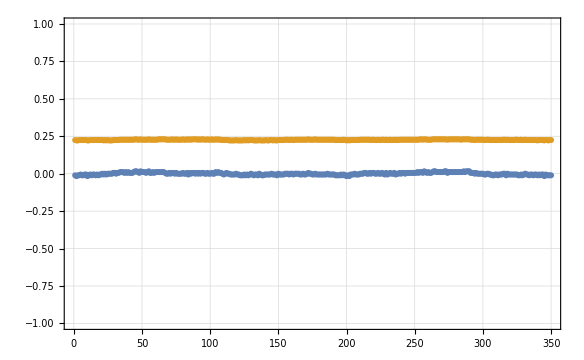

```mathematica
ListPlot[{dichroism,voltage},PlotRange->{-1,1}]
```